```mathematica
<<JLink`
```

```mathematica
LoadJavaClass["java.awt.geom.Ellipse2D"];
```

```mathematica
LoadJavaClass["java.awt.geom.PathIterator"];
```

```mathematica
circle=JavaNew["java.awt.geom.Ellipse2D$Double",100.0,100.0,100.0,100.0]
```

«JavaObject[java.awt.geom.Ellipse2D$Double]»

```mathematica
renderJavaShape[shape_]:=(
lastPoint=Null;
graphics={};
coordsObj=JavaNew["[D",6];
pi=shape@getPathIterator[Null];
While[!pi@isDone[],
res=pi@currentSegment[coordsObj];
coords=JavaObjectToExpression[coordsObj];
Switch[res,
PathIterator`SEGUMOVETO,
lastPoint=coords[[1;;2]];
,
PathIterator`SEGUCLOSE,,
PathIterator`SEGULINETO,,
PathIterator`SEGUQUADTO,,
PathIterator`SEGUCUBICTO,
graphics=graphics~Append~BezierCurve[{lastPoint}~Join~Partition[coords,2]];
lastPoint=coords[[5;;6]]
];
pi@next[]
];
graphics
)
```

```mathematica
renderJavaShape[circle]
```

{BezierCurve[{{200.,150.},{200.,177.614},{177.614,200.},{150.,200.}}],BezierCurve[{{150.,200.},{122.386,200.},{100.,177.614},{100.,150.}}],BezierCurve[{{100.,150.},{100.,122.386},{122.386,100.},{150.,100.}}],BezierCurve[{{150.,100.},{177.614,100.},{200.,122.386},{200.,150.}}]}

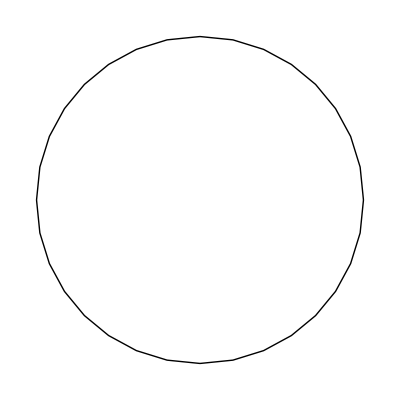

```mathematica
Graphics[%]
```

```mathematica
custom=JavaNew["java.awt.geom.GeneralPath"]
```

«JavaObject[java.awt.geom.GeneralPath]»

```mathematica
custom@moveTo[200,150]
```

```mathematica
custom@curveTo[200.,177.61423749153965,177.61423749153965,200.,150.,200.]
custom@curveTo[122.38576250846033,200.,100.,177.61423749153965,100.,150.]
custom@curveTo[100.,122.38576250846033,122.38576250846033,100.,150.,100.]
custom@curveTo[177.61423749153965,100.,200.,122.38576250846033,200.,150.]
```

```mathematica
custom@closePath[]
```

```mathematica
Graphics[renderJavaShape[custom]]
```

-Graphics-

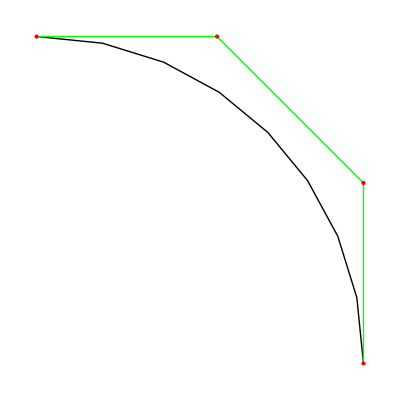

```mathematica
pts={{200,150},{200.,177.61423749153965},{177.61423749153965,200.},{150.,200.}};
Graphics[{BezierCurve[pts],Green,Line[pts],Red,Point[pts]}]
```